## Wood-Saxon

```mathematica
RA[A_]:=112/100 A^(1/3)-86/100 A^(-1/3)
d=54/100;
n0[A_]:=3/4 A/(π RA[A]^3)1/(1+((π d)/RA[A])^2)
ρ0=17/100;
```

```mathematica
integrand[s_,z_,A_]:=n0[A]/(1+Exp[(√(s^2+z^2)-RA[A])/d])
```

```mathematica
ρ[r_,A_]:=ρ0/(1+Exp[(r-RA[A])/d])
ρ[s_,z_,A_]:=ρ[√(s^2+z^2),A]
```

```mathematica
TA[s_?NumericQ,A_?NumericQ]:=NIntegrate[integrand[s,z,A],{z,-∞,∞}]
```

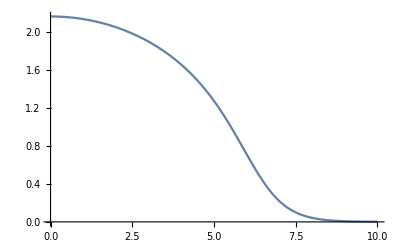

```mathematica
Plot[TA[s,197],{s,0,10}]
```

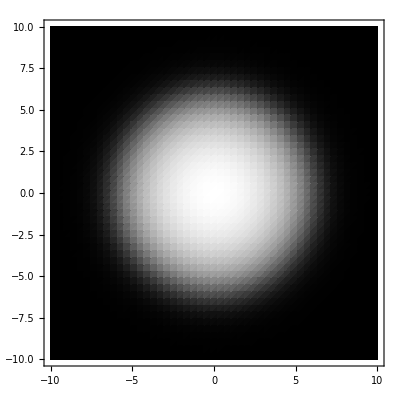

```mathematica
DensityPlot[TA[Norm[{sx,sy}],197],{sx,-10,10},{sy,-10,10},PlotPoints->50,ColorFunction->GrayLevel]
```

```mathematica
total[A_]=Integrate[integrand[Norm[{sx,sy}],z,A],{z,-∞,∞},{sx,-∞,∞},{sy,-∞,∞}]
```

-(118098 A^2 PolyLog[3,-ⅇ^((-43+56 A^(2/3))/(27 A^(1/3)))])/((-43+56 A^(2/3)) (1849-4816 A^(2/3)+3136 A^(4/3)+729 A^(2/3) π^2))

```mathematica
total[1]//N
total[197]//N
```

1.71198

197.

```mathematica
NIntegrate[(TA[Norm[{sx,sy}],27])^2,{sx,-∞,∞},{sy,-∞,∞}]//Quiet
```

17.0053

```mathematica
NIntegrate[(TA[Norm[{sx,sy}],197])^2,{sx,-∞,∞},{sy,-∞,∞}]//Quiet
```

293.534

```mathematica
UnitConvert[Quantity[17.0053,1/("Femtometers")^2],1/"Millibarns"]
```

1.70053 /mb